# Midiendo la ergodicidad y comparando con MH con Brutal

```mathematica
Get["/media/storage/ciencia/investigacion/tesis/codigos-tesis/CoolTools2.m"]
Get["/media/storage/ciencia/investigacion/tesis/codigos-tesis/usefulFunctions.wl"]
<<"MaTeX`"
```

## Midiendo la ergodicidad

La ergodicidad puede entenderse como la idea de que el muestreo visita eventualmente toda la región de interés. Sabemos que el muestreo resultante del algoritmo Brutal es certero y, por lo tanto, ergódico. Entonces, para saber si el muestreo con el MH es ergódico, tiene sentido compararlo con el muestreo brutal de alguna manera. Para ello, tomaremos una muestra brutal de referencia con, digamos, 100 puntos. A los puntos de esa muestra se les medirá la distancia a los puntos de una muestra MH en cuestión y se tomará la más chica (por ahora. Vamos a probar de qué manera se mide mejor).

### Medida de ergodicidad

Las funciones necesarias para calcular ergodicidades ya se encuentran en el archivo usefulFunctions.wl. Cabe mencionar que se conservaron las medidas 2 (promedio) y 4 (norma infinito); las demás se abandonaron. Los detalles sobre cómo funcionan estas medidas de ergodicidad puede verse en el cuaderno de notas (o en la tesis misma, eventualmente).

### Ergodicidad de las muestras brutales

Las muestras brutales son las de mejor ergodicidad, por lo que al medir ésta última tendremos un valor “ideal” respecto al cual comparar. En este momento, tenemos 4 muestras brutales distintas: aquella de la que se tomaron los estados de referencia y otras tres adicionales. Calcularemos la ergodicidad de todas ellas, para todos los r_z y todas las swapPs. NOTA al 30 de junio de 2022: Sólo se calcularán las ergodicidades 2 y 4 que corresponden al promedio y a la norma infinito respectivamente, las demás fueron descontinuadas.

```mathematica
SetDirectory["/media/storage/ciencia/investigacion/tesis/muestras_brutales_extra"]
```

/media/storage/ciencia/investigacion/tesis/muestras_brutales_extra

#### Primera muestra (la de referencia)

Como esta es la muestra de donde se obtienen las referencias, todas las medidas de ergodicidad resultarán cero, excepto la quinta, que dará 1. Esto sucederá siempre que los puntos de referencia estén incluidos también en la muestra cuya ergodicidad se medirá sin importar el tamaño de ésta última; pues el vector de mínimas distancias será un vector de ceros. 
Ahora mismo, el tamaño de las muestras de referencia es N = 100.

```mathematica
(*Referencias para Subscript[r, z] = 0*)
brutalRefR0Pp3=ketsToDensity[<<"/media/storage/ciencia/investigacion/adanerick/muestras_de_edos/pureBrutalStates/pureHaarStates_n=10000_p=0.3_rz=0.m"⟦1;;300⟧];
brutalRefR0Pp5=ketsToDensity[<<"/media/storage/ciencia/investigacion/adanerick/muestras_de_edos/pureBrutalStates/pureHaarStates_n=10000_p=0.5_rz=0.m"⟦1;;300⟧];
brutalRefR0Pp8=ketsToDensity[<<"/media/storage/ciencia/investigacion/adanerick/muestras_de_edos/pureBrutalStates/pureHaarStates_n=10000_p=0.8_rz=0.m"⟦1;;300⟧];
```

```mathematica
(*Referencias para Subscript[r, z] = 0.5*)
brutalRefRp5Pp3=ketsToDensity[<<"/media/storage/ciencia/investigacion/adanerick/muestras_de_edos/pureBrutalStates/pureHaarStates_n=10000_p=0.3_rz=0.5.m"⟦1;;500⟧];
brutalRefRp5Pp5=ketsToDensity[<<"/media/storage/ciencia/investigacion/adanerick/muestras_de_edos/pureBrutalStates/pureHaarStates_n=10000_p=0.5_rz=0.5.m"⟦1;;500⟧];
brutalRefRp5Pp8=ketsToDensity[<<"/media/storage/ciencia/investigacion/adanerick/muestras_de_edos/pureBrutalStates/pureHaarStates_n=10000_p=0.8_rz=0.5.m"⟦1;;500⟧];
```

```mathematica
(*Referencias para Subscript[r, z] = 0.8*)¨
brutalRefRp8Pp3=ketsToDensity[<<"/media/storage/ciencia/investigacion/adanerick/muestras_de_edos/pureBrutalStates/pureHaarStates_n=10000_p=0.3_rz=0.8.m"⟦1;;100⟧];
brutalRefRp8Pp5=ketsToDensity[<<"/media/storage/ciencia/investigacion/adanerick/muestras_de_edos/pureBrutalStates/pureHaarStates_n=10000_p=0.5_rz=0.8.m"⟦1;;100⟧];
brutalRefRp8Pp8=ketsToDensity[<<"/media/storage/ciencia/investigacion/adanerick/muestras_de_edos/pureBrutalStates/pureHaarStates_n=10000_p=0.8_rz=0.8.m"⟦1;;100⟧];
```

#### Juntando todas las muestras

La muestra de referencia es considerada como la muestra Brutal 1. Por esa razón, las otras tres muestras están etiquetadas en lo que sigue como “brutals2”, “brutals3” y “brutals4”.

```mathematica
(*Importando muestras Brutales 2. Para toda Subscript[r, z] y toda p*)
brutals2R0allP=(ketsToDensity[#1]&)/@<<"brutalSamples_rz=0_N=7000_eps=0.01_allswapPs.m";
brutals2Rp5allP=(ketsToDensity[#1]&)/@<<"brutalSamples_rz=0.5_N=7000_eps=0.01_allswapPs.m";
brutals2Rp8allP=(ketsToDensity[#1]&)/@<<"brutalSamples_rz=0.8_N=7000_eps=0.01_allswapPs.m";
```

```mathematica
(*Importando muestras Brutales 3. Para toda Subscript[r, z] y toda p*)
brutals3R0allP=(ketsToDensity[#1]&)/@<<"brutalSamples2_rz=0_N=7000_eps=0.01_allswapPs.m";
brutals3Rp5allP=(ketsToDensity[#1]&)/@<<"brutalSamples2_rz=0.5_N=7000_eps=0.01_allswapPs.m";
brutals3Rp8allP=(ketsToDensity[#1]&)/@<<"brutalSamples2_rz=0.8_N=7000_eps=0.01_allswapPs.m";
```

```mathematica
(*Importando muestras Brutales 4. Para toda Subscript[r, z] y toda p*)
brutals4R0allP=(ketsToDensity[#1]&)/@<<"brutalSamples3_rz=0_N=10000_eps=0.01_allswapPs.m";
brutals4Rp5allP=(ketsToDensity[#1]&)/@<<"brutalSamples3_rz=0.5_N=10000_eps=0.01_allswapPs.m";
brutals4Rp8allP=(ketsToDensity[#1]&)/@<<"brutalSamples3_rz=0.8_N=10000_eps=0.01_allswapPs.m";
```

```mathematica
(*Juntando todos los edos brutales para Subscript[r, z] = 0 y toda p*)
brutalsAllR0Pp3 = Join[brutals2R0allP[[1]], brutals3R0allP[[1]], brutals4R0allP[[1]]];
brutalsAllR0Pp5 = Join[brutals2R0allP[[2]], brutals3R0allP[[2]], brutals4R0allP[[2]]];
brutalsAllR0Pp8 = Join[brutals2R0allP[[3]], brutals3R0allP[[3]], brutals4R0allP[[3]]];
Clear[brutals2R0allP, brutals3R0allP, brutals4R0allP]
```

```mathematica
(*Juntando todos los edos brutales para Subscript[r, z] = 0.5 y toda p*)
brutalsAllRp5Pp3 = Join[brutals2Rp5allP[[1]], brutals3Rp5allP[[1]], brutals4Rp5allP[[1]]];
brutalsAllRp5Pp5 = Join[brutals2Rp5allP[[2]], brutals3Rp5allP[[2]], brutals4Rp5allP[[2]]];
brutalsAllRp5Pp8 = Join[brutals2Rp5allP[[3]], brutals3Rp5allP[[3]], brutals4Rp5allP[[3]]];
Clear[brutals2Rp5allP, brutals3Rp5allP, brutals4Rp5allP]
```

```mathematica
(*Juntando todos los edos brutales para Subscript[r, z] = 0.8 y toda p*)
brutalsAllRp8Pp3 = Join[brutals2Rp8allP[[1]], brutals3Rp8allP[[1]], brutals4Rp8allP[[1]]];
brutalsAllRp8Pp5 = Join[brutals2Rp8allP[[2]], brutals3Rp8allP[[2]], brutals4Rp8allP[[2]]];
brutalsAllRp8Pp8 = Join[brutals2Rp8allP[[3]], brutals3Rp8allP[[3]], brutals4Rp8allP[[3]]];
Clear[brutals2Rp8allP, brutals3Rp8allP, brutals4Rp8allP]
```

```mathematica
(*vectores de mínimas distancias para cada Subscript[r, z] y p, para distintas N's*)
minVecsR0allP =(MapThread[minDistancesVector[#1,#2]&,{{brutalRefR0Pp3,brutalRefR0Pp5,brutalRefR0Pp8},#1}]&)/@Outer[#2⟦1;;#1⟧&,Table[1000 i,{i,24}],{brutalsAllR0Pp3, brutalsAllR0Pp5, brutalsAllR0Pp8},1];
minVecsRp5allP =(MapThread[minDistancesVector[#1,#2]&,{{brutalRefRp5Pp3,brutalRefRp5Pp5,brutalRefRp5Pp8},#1}]&)/@Outer[#2⟦1;;#1⟧&,Table[1000 i,{i,24}],{brutalsAllRp5Pp3, brutalsAllRp5Pp5, brutalsAllRp5Pp8},1];
minVecsRp8allP =(MapThread[minDistancesVector[#1,#2]&,{{brutalRefRp8Pp3,brutalRefRp8Pp5,brutalRefRp8Pp8},#1}]&)/@Outer[#2⟦1;;#1⟧&,Table[1000 i,{i,24}],{brutalsAllRp8Pp3, brutalsAllRp8Pp5, brutalsAllRp8Pp8},1];
(*ya fueron exportados*)
```

```mathematica
(*importamos los minVecs en vez de calcularlos como la primera vez*)
minVecsR0allP = Get["brutalsMinVecsR0allP_maxN24000.wl"];
minVecsRp5allP = Get["brutalsMinVecsRp5allP_maxN24000.wl"];
minVecsRp8allP = Get["brutalsMinVecsRp8allP_maxN24000.wl"];
```

```mathematica
Dimensions[minVecsR0allP]
```

{24,3,100}

#### Acá pondremos lo necesario para tomar en cuenta la ejecución de emergencia (r_z = 0.5, p = 0.3, N = 100 000)

```mathematica
SetDirectory["/media/storage/ciencia/trabajo-con-carlos/tesis"]
```

/media/storage/ciencia/trabajo-con-carlos/tesis

```mathematica
Directory[]
```

/media/storage/ciencia/trabajo-con-carlos/tesis

```mathematica
extraDists = {};
```

```mathematica
brutals2Rp5allP=(ketsToDensity[#1]&)/@<<"muestras_brutales_extra/brutalSamples_rz=0.5_N=7000_eps=0.01_allswapPs.m";
brutals3Rp5allP=(ketsToDensity[#1]&)/@<<"muestras_brutales_extra/brutalSamples2_rz=0.5_N=7000_eps=0.01_allswapPs.m";
brutals4Rp5allP=(ketsToDensity[#1]&)/@<<"muestras_brutales_extra/brutalSamples3_rz=0.5_N=10000_eps=0.01_allswapPs.m";
firstBrutalsRp5Pp3 = Join[brutals2Rp5allP[[1]], brutals3Rp5allP[[1]], brutals4Rp5allP[[1]]];
Clear[brutals2Rp5allP, brutals3Rp5allP, brutals4Rp5allP]
```

```mathematica
extraBrutals = Flatten[Map[ketsToDensity[Get["brutals_"<>ToString[#]<>".wl"][[2]]]&, Table[i,{i,16}]], 1];
```

```mathematica
(*unimos ambas listas:*)
allBrutalsRp5Pp3 = Join[firstBrutalsRp5Pp3, extraBrutals];
Clear[firstBrutalsRp5Pp3, extraBrutals]
```

```mathematica
Dimensions[allBrutalsRp5Pp3]
```

{104000,4,4}

```mathematica
Table[i,{i,30000, 104000, 10000}]
```

{30000,40000,50000,60000,70000,80000,90000,100000}

```mathematica
(*Ahora, a calcular la ergodicidad de la muestra con 104 000 estados:*)
extraMinVecsRp5Pp3 = Map[minDistancesVector[brutalRefRp5Pp3, allBrutalsRp5Pp3[[1;;#]]]&, Table[i,{i,30000,104000,10000}]];
```

```mathematica
Clear[allBrutalsRp5Pp3]
```

```mathematica
(*ERgodiciidades para rz = 0.5, p = 0.3*)
minVecsRp5Pp3 = Join[Map[#[[1]]&, Get["brutalsMinVecsRp5allP_maxN24000.wl"]], extraMinVecsRp5Pp3];
Clear[extraMinVecsRp5Pp3]
```

```mathematica
ergs2brutalsRp5Pp3 = Map[ergodicityMeasure2[#]&, minVecsRp5Pp3];
ergs4brutalsRp5Pp3 = Map[ergodicityMeasure4[#]&, minVecsRp5Pp3];
```

```mathematica
(*corresponding sample sizes*)
sizes = Join[Table[1000 i, {i,24}], Table[i, {i, 30000,104000,10000}]]
```

```mathematica
erg2DataRp5Pp3 = MapThread[{#1, #2}&, {sizes, ergs2brutalsRp5Pp3}];
erg4DataRp5Pp3 = MapThread[{#1, #2}&, {sizes, ergs4brutalsRp5Pp3}];
```

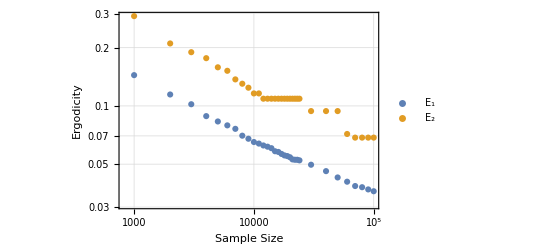

```mathematica
ListLogLogPlot[{erg2DataRp5Pp3, erg4DataRp5Pp3}, PlotTheme->"Detailed", PlotRange->Full, 
				PlotLegends->PointLegend[{"E_1", "E_2"}, LabelStyle->Black], 
				FrameLabel->{"Sample Size", "Ergodicity"}, FrameStyle->Black]
```

```mathematica
Export["ergodicities_with_many_brutals.pdf",%310]
```

ergodicities_with_many_brutals.pdf

#### Ergodicidades de los brutales (sin las muestras de emergencia)

Ergodicidad 2

```mathematica
ergs2brutalsR0allP=Map[ergodicityMeasure2[#1]&,minVecsR0allP,{2}];
ergs2brutalsRp5allP=Map[ergodicityMeasure2[#1]&,minVecsRp5allP,{2}];
ergs2brutalsRp8allP=Map[ergodicityMeasure2[#1]&,minVecsRp8allP,{2}];
```

Ergodicidad 4

```mathematica
ergs4brutalsR0allP=Map[ergodicityMeasure4[#1]&,minVecsR0allP,{2}];
ergs4brutalsRp5allP=Map[ergodicityMeasure4[#1]&,minVecsRp5allP,{2}];
ergs4brutalsRp8allP=Map[ergodicityMeasure4[#1]&,minVecsRp8allP,{2}];
```

Ahora, comparemos todas las ergodicidades para cada caso:

```mathematica
enes = Table[1000 i, {i,1,24}];
```

```mathematica
erg2DataR0allP = Map[MapThread[{#1,#2}&, {enes, #}]&, Transpose[ergs2brutalsR0allP]];
erg2DataRp5allP = Map[MapThread[{#1,#2}&, {enes, #}]&, Transpose[ergs2brutalsRp5allP]];
erg2DataRp8allP = Map[MapThread[{#1,#2}&, {enes, #}]&, Transpose[ergs2brutalsRp8allP]];
```

```mathematica
erg4DataR0allP = Map[MapThread[{#1,#2}&, {enes, #}]&, Transpose[ergs4brutalsR0allP]];
erg4DataRp5allP = Map[MapThread[{#1,#2}&, {enes, #}]&, Transpose[ergs4brutalsRp5allP]]; 
erg4DataRp8allP = Map[MapThread[{#1,#2}&, {enes, #}]&, Transpose[ergs4brutalsRp8allP]];
```

Primero graficamos la ergodicidad en función de N para cada target y cada swapP:

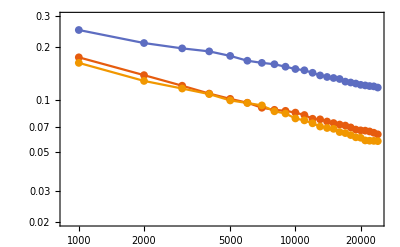
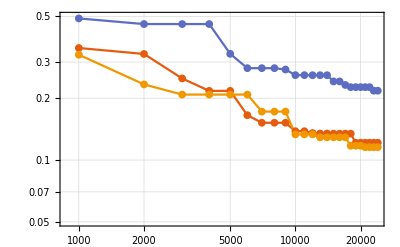
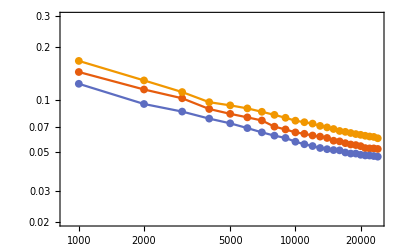
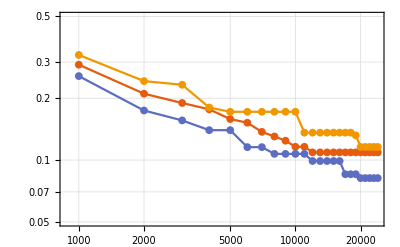
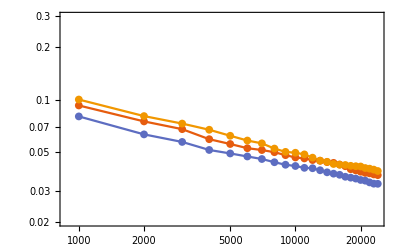
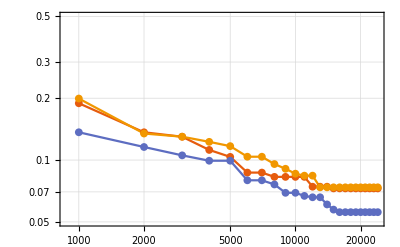
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
Grid[{{ListLogLogPlot[erg2DataR0allP, PlotTheme->"Scientific", FrameLabel->MaTeX[{"\\text{Tamaño de la preimagen}", "\\tilde{E}_1"}, Preamble->{"\\usepackage{newtxmath}"}],
					PlotLabel->MaTeX["r_z = 0", Preamble->{"\\usepackage{newtxmath}"}],
					PlotRange->{0.02, 0.3},
					FrameStyle->Black,
					GridLines->Automatic, Joined->True, Mesh->All, MeshStyle->PointSize[0.014]],
		ListLogLogPlot[erg4DataR0allP, PlotTheme->"Scientific", FrameLabel->MaTeX[{"\\text{Tamaño de la preimagen}", "\\tilde{E}_2"}, Preamble->{"\\usepackage{newtxmath}"}],
	                PlotLegends->PointLegend[MaTeX[{0.3,0.5,0.8}], LegendLabel->MaTeX["p", Preamble->{"\\usepackage{newtxmath}"}]],
					PlotLabel->MaTeX["r_z = 0", Preamble->{"\\usepackage{newtxmath}"}],
					PlotRange->{0.05, 0.5},
					FrameStyle->Black,
					GridLines->Automatic, Joined->True, Mesh->All, MeshStyle->PointSize[0.014]]},
	   {ListLogLogPlot[erg2DataRp5allP, PlotTheme->"Scientific", FrameLabel->MaTeX[{"\\text{Tamaño de la preimagen}", "\\tilde{E}_1"}, Preamble->{"\\usepackage{newtxmath}"}],
					PlotLabel->MaTeX["r_z = 0.5", Preamble->{"\\usepackage{newtxmath}"}],
					PlotRange->{0.02, 0.3},
					FrameStyle->Black,
					GridLines->Automatic, Joined->True, Mesh->All, MeshStyle->PointSize[0.014]],
		ListLogLogPlot[erg4DataRp5allP, PlotTheme->"Scientific", FrameLabel->MaTeX[{"\\text{Tamaño de la preimagen}", "\\tilde{E}_2"}, Preamble->{"\\usepackage{newtxmath}"}],
	                PlotLegends->PointLegend[MaTeX[{0.3,0.5,0.8}], LegendLabel->MaTeX["p", Preamble->{"\\usepackage{newtxmath}"}]],
					PlotLabel->MaTeX["r_z = 0.5", Preamble->{"\\usepackage{newtxmath}"}],
					PlotRange->{0.05, 0.5},
					FrameStyle->Black,
					GridLines->Automatic, Joined->True, Mesh->All, MeshStyle->PointSize[0.014]]},
	   {ListLogLogPlot[erg2DataRp8allP, PlotTheme->"Scientific", FrameLabel->MaTeX[{"\\text{Tamaño de la preimagen}", "\\tilde{E}_1"}, Preamble->{"\\usepackage{newtxmath}"}],
					PlotLabel->MaTeX["r_z = 0.8", Preamble->{"\\usepackage{newtxmath}"}],
					PlotRange->{0.02, 0.3},
					FrameStyle->Black,
					GridLines->Automatic, Joined->True, Mesh->All, MeshStyle->PointSize[0.014]],
		ListLogLogPlot[erg4DataRp8allP, PlotTheme->"Scientific", FrameLabel->MaTeX[{"\\text{Tamaño de la preimagen}", "\\tilde{E}_2"}, Preamble->{"\\usepackage{newtxmath}"}],
					PlotLegends->PointLegend[MaTeX[{0.3,0.5,0.8}], LegendLabel->MaTeX["p", Preamble->{"\\usepackage{newtxmath}"}]],
					PlotLabel->MaTeX["r_z = 0.8", Preamble->{"\\usepackage{newtxmath}"}],
					PlotRange->{0.05, 0.5},
					FrameStyle->Black,
					GridLines->Automatic, Joined->True, Mesh->All, MeshStyle->PointSize[0.014]]}
}, ItemSize->Automatic, ItemStyle->ImageSizeMultipliers->1, Spacings->{1, 1}]
```

```mathematica
Export["brutalErgodicities_allRallP.pdf", %272]
```

brutalErgodicities_allRallP.pdf

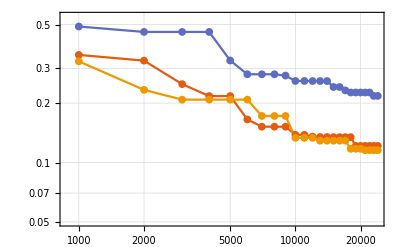
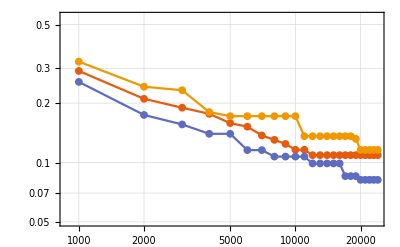
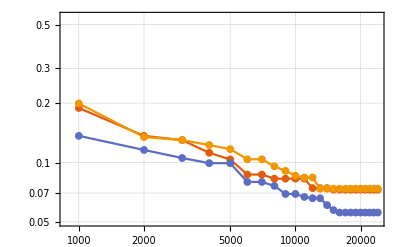
-Graphics- | -Graphics- | -Graphics-

```mathematica
Grid[{{ListLogLogPlot[erg4DataR0allP, PlotTheme->"Scientific", FrameLabel->MaTeX[{"\\text{Iteraciones}", "E_2"}, Preamble->{"\\usepackage{newtxmath}"}],
	                PlotLegends->PointLegend[MaTeX[{0.3,0.5,0.8}], LegendLabel->MaTeX["p", Preamble->{"\\usepackage{newtxmath}"}]],
					PlotLabel->MaTeX["r_z = 0", Preamble->{"\\usepackage{newtxmath}"}],
					PlotRange->{0.05, 0.55},
					FrameStyle->Black,
					GridLines->Automatic, Joined->True, Mesh->All, MeshStyle->PointSize[0.014]],
	   ListLogLogPlot[erg4DataRp5allP, PlotTheme->"Scientific", FrameLabel->MaTeX[{"\\text{Iteraciones}", "E_2"}, Preamble->{"\\usepackage{newtxmath}"}],
	                PlotLegends->PointLegend[MaTeX[{0.3,0.5,0.8}], LegendLabel->MaTeX["p", Preamble->{"\\usepackage{newtxmath}"}]],
					PlotLabel->MaTeX["r_z = 0.5", Preamble->{"\\usepackage{newtxmath}"}],
					PlotRange->{0.05, 0.55},
					FrameStyle->Black,
					GridLines->Automatic, Joined->True, Mesh->All, MeshStyle->PointSize[0.014]],
	   ListLogLogPlot[erg4DataRp8allP, PlotTheme->"Scientific", FrameLabel->MaTeX[{"\\text{Iteraciones}", "E_2"}, Preamble->{"\\usepackage{newtxmath}"}],
					PlotLegends->PointLegend[MaTeX[{0.3,0.5,0.8}], LegendLabel->MaTeX["p", Preamble->{"\\usepackage{newtxmath}"}]],
					PlotLabel->MaTeX["r_z = 0.8", Preamble->{"\\usepackage{newtxmath}"}],
					PlotRange->{0.05, 0.55},
					FrameStyle->Black,
					GridLines->Automatic, Joined->True, Mesh->All, MeshStyle->PointSize[0.014]]}
}]
(*Ergodicidad 2 en función de N para cada target. Se muestra cada p en cada gráfica también*)
```

Ahora, graficamos juntas Erg 1 y Erg 2

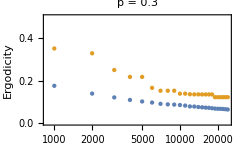
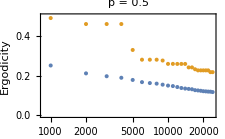
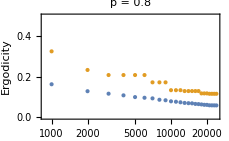
-Graphics- | -Graphics- | -Graphics- |

```mathematica
swapPs = {0.3, 0.5, 0.8};
Grid[{Append[ListLogLinearPlot[{erg2DataR0allP[[#]], erg4DataR0allP[[#]]}, 
							   PlotRange->{0,0.5},
							   PlotTheme->"Detailed", 
							   FrameLabel->{"Sample size","Ergodicity"}, 
							   PlotLabel->"p = "<>ToString[swapPs[[#]]]]& /@ {1,2,3}, 
			 PointLegend[97,{"E_1", "E_2"}]]
}]
(*Ambas ergs. para rz = 0 y toda p*)
```

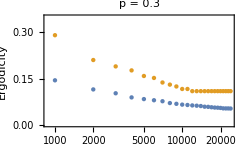
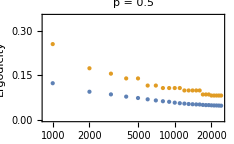
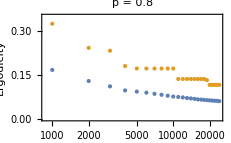
-Graphics- | -Graphics- | -Graphics- |

```mathematica
Grid[{Append[ListLogLinearPlot[{erg2DataRp5allP[[#]], erg4DataRp5allP[[#]]},
							   PlotRange->{0,0.35}, 
							   PlotTheme->"Detailed", 
							   FrameLabel->{"Sample size","Ergodicity"}, 
							   PlotLabel->"p = "<>ToString[swapPs[[#]]]]& /@ {1,2,3}, 
			 PointLegend[97,{"E_1", "E_2"}]]
}]
(*Ambas ergs. para rz = 0.5 y toda p*)
```

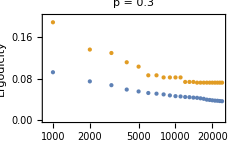
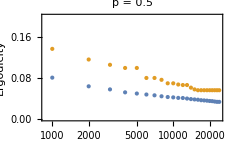
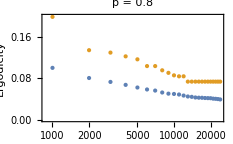
-Graphics- | -Graphics- | -Graphics- |

```mathematica
Grid[{Append[ListLogLinearPlot[{erg2DataRp8allP[[#]], erg4DataRp8allP[[#]]},
							   PlotRange->{0,0.2}, 
							   PlotTheme->"Detailed", 
							   FrameLabel->{"Sample size","Ergodicity"}, 
							   PlotLabel->"p = "<>ToString[swapPs[[#]]]]& /@ {1,2,3}, 
			 PointLegend[97,{"E_1", "E_2"}]]
}]
(*Ambas ergs. para rz = 0.8 y toda p*)
```

#### Ergodicidades de los brutales “bien medidas”

```mathematica
minVecsR0Pp3allN = minDistancesVector[brutalRefR0Pp3, #]& /@ (RandomSample[brutalsAllR0Pp3, #]& /@ enes);
minVecsR0Pp5allN = minDistancesVector[brutalRefR0Pp5, #]& /@ (RandomSample[brutalsAllR0Pp5, #]& /@ enes);
minVecsR0Pp8allN = minDistancesVector[brutalRefR0Pp8, #]& /@ (RandomSample[brutalsAllR0Pp8, #]& /@ enes);
```

```mathematica
ergs2R0Pp3 = MapThread[{#1, #2}&, {enes, (ergodicityMeasure2[#]& /@ minVecsR0Pp3allN)}];
ergs2R0Pp5 = MapThread[{#1, #2}&, {enes, (ergodicityMeasure2[#]& /@ minVecsR0Pp5allN)}];
ergs2R0Pp8 = MapThread[{#1, #2}&, {enes, (ergodicityMeasure2[#]& /@ minVecsR0Pp8allN)}];
```

```mathematica
ergs4R0Pp3 = MapThread[{#1, #2}&, {enes, (ergodicityMeasure4[#]& /@ minVecsR0Pp3allN)}];
ergs4R0Pp5 = MapThread[{#1, #2}&, {enes, (ergodicityMeasure4[#]& /@ minVecsR0Pp5allN)}];
ergs4R0Pp8 = MapThread[{#1, #2}&, {enes, (ergodicityMeasure4[#]& /@ minVecsR0Pp8allN)}];
```

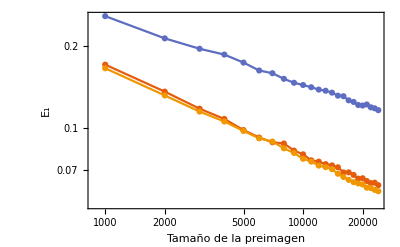
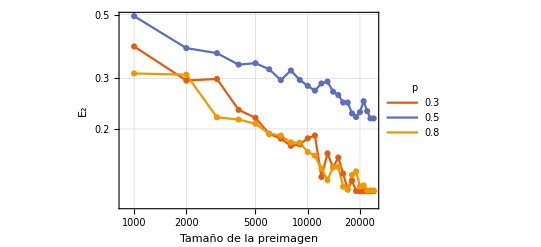
-Graphics- | -Graphics-

```mathematica
Grid[{{ListLogLogPlot[{ergs2R0Pp3, ergs2R0Pp5, ergs2R0Pp8}, PlotTheme->"Scientific", GridLines->Automatic, Joined->True, Mesh->All,
					   FrameLabel->{"Tamaño de la preimagen", "E_1"}], 
       ListLogLogPlot[{ergs4R0Pp3, ergs4R0Pp5, ergs4R0Pp8}, PlotTheme->"Scientific", GridLines->Automatic, Joined->True, Mesh->All,
                       FrameLabel->{"Tamaño de la preimagen", "E_2"}, PlotLegends->LineLegend[{0.3, 0.5, 0.8}, LegendLabel->"p"]]}
}, ItemStyle->ImageSizeMultipliers->1, Spacings->{1, 1}]
```

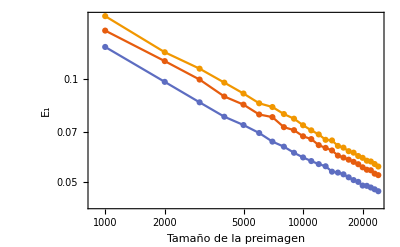
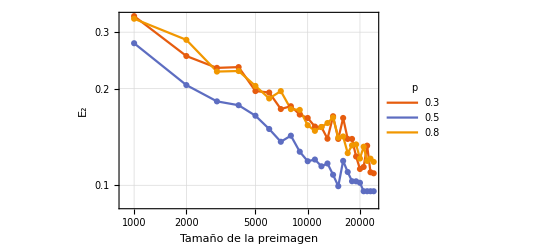
-Graphics- | -Graphics-

```mathematica
Grid[{{ListLogLogPlot[{ergs2Rp5Pp3, ergs2Rp5Pp5, ergs2Rp5Pp8}, PlotTheme->"Scientific", GridLines->Automatic, Joined->True, Mesh->All,
					   FrameLabel->{"Tamaño de la preimagen", "E_1"}], 
       ListLogLogPlot[{ergs4Rp5Pp3, ergs4Rp5Pp5, ergs4Rp5Pp8}, PlotTheme->"Scientific", GridLines->Automatic, Joined->True, Mesh->All,
                       FrameLabel->{"Tamaño de la preimagen", "E_2"}, PlotLegends->LineLegend[{0.3, 0.5, 0.8}, LegendLabel->"p"]]}
}, ItemStyle->ImageSizeMultipliers->1, Spacings->{1, 1}]
```

Parece que, aunque las preimágenes brutales sean tomadas con aleatoriedad, la erg2 se sigue comportando raro. De hecho, se comporta más raro aún por los picos que salen. La explicación de lo feo que sale es quizá la misma que está en la tesis. Entonces, me sigo inclinando por el uso de la erg 1.

## Determinación de los tiempos (tamaños) críticos del MH

A partir de los resultados obtenidos de la ergodicidad de las muestras brutales, tenemos ya una idea de qué valores de ergodicidad son los que buscamos. Nuestro objetivo es determinar el tamaño de muestra N en el algoritmo MH que nos dé ergodicidades como las del Brutal. Es de esperarse que estos tiempos críticos dependan de β y δ (y posiblemente también de r_z y p).

### Primera medición de ergodicidades para muestras MH

Por ahora nos limitaremos al caso β = 500, δ = 0.01, pues el error es decente así como el tiempo de ejecución del algoritmo .

```mathematica
enes = {10000,30000,50000,70000,90000,100000,120000,150000,170000,20000};
```

```mathematica
minDistancesVecsRp5Pp3δp01 = MapMonitored[minDistancesVector[brutalRefRp5Pp3, Get["MHsample_N="<>ToString[#]<>"_rz=0.5_p=0.3.wl"][[2]]]&, enes];
```

```mathematica
(*ergs1 = Map[ergodicityMeasure1[#]&, minDistancesVecsRp5Pp3];*)
ergs2δp01 = Map[ergodicityMeasure2[#]&, minDistancesVecsRp5Pp3δp01];
(*ergs3 = Map[ergodicityMeasure3[#]&, minDistancesVecsRp5Pp3];*)
ergs4δp01 = Map[ergodicityMeasure4[#]&, minDistancesVecsRp5Pp3δp01];
(*ergs5 = Map[ergodicityMeasure5[#]&, minDistancesVecsRp5Pp3];*)
```

```mathematica
(*ergs1 =MapThread[{#1, #2}&, {enes, ergs1}];*)
ergs2δp01 =MapThread[{#1, #2}&, {enes, ergs2δp01}];
(*ergs3 =MapThread[{#1, #2}&, {enes, ergs3}];*)
ergs4δp01 =MapThread[{#1, #2}&, {enes, ergs4δp01}];
(*ergs5 =MapThread[{#1, #2}&, {enes, ergs5}];*)
```

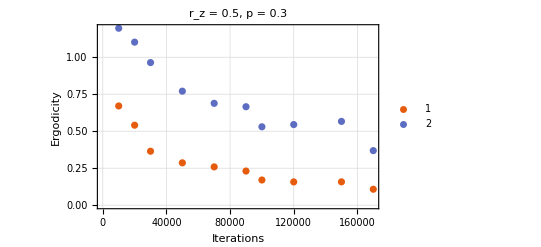

```mathematica
ListPlot[{ergs2, ergs4}, PlotTheme->"Scientific", GridLines->Automatic, PlotLegends->{1,2}, FrameLabel->{"Iterations", "Ergodicity"}, PlotLabel->"r_z = 0.5, p = 0.3"]
```

```mathematica
Export["ergsMH_rz=0p5_p=0p3.png",%171]
```

ergsMH_rz=0p5_p=0p3.png

```mathematica
(*rz = 0.5, p  =0.3, β=500 y δ = 0.001*)
minDistancesVecsRp5Pp3δp001 = MapMonitored[minDistancesVector[brutalRefRp5Pp3, Get["MHsample_N="<>ToString[#]<>"_delta=0.001_rz=0.5_p=0.3.wl"][[2]]]&, enes];
```

```mathematica
ergs2δp001 = Map[ergodicityMeasure2[#]&, minDistancesVecsRp5Pp3δp001];
ergs4δp001 = Map[ergodicityMeasure4[#]&, minDistancesVecsRp5Pp3δp001];
```

```mathematica
ergs2δp001 =MapThread[{#1, #2}&, {enes, ergs2δp001}];
ergs4δp001 =MapThread[{#1, #2}&, {enes, ergs4δp001}];
```

```mathematica
(*rz = 0.5, p  =0.3, β=500 y δ = 0.02*)
minDistancesVecsRp5Pp3δp02 = MapMonitored[minDistancesVector[brutalRefRp5Pp3, Get["MHsample_N="<>ToString[#]<>"_delta=0.02_rz=0.5_p=0.3.wl"][[2]]]&, enes];
```

```mathematica
ergs2δp02 = Map[ergodicityMeasure2[#]&, minDistancesVecsRp5Pp3δp02];
ergs4δp02 = Map[ergodicityMeasure4[#]&, minDistancesVecsRp5Pp3δp02];
```

```mathematica
ergs2δp02 =MapThread[{#1, #2}&, {enes, ergs2δp02}];
ergs4δp02 =MapThread[{#1, #2}&, {enes, ergs4δp02}];
```

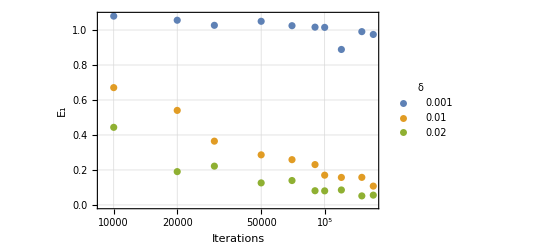

```mathematica
ListLogLinearPlot[{ergs2δp001, ergs2δp01, ergs2δp02}, PlotTheme->"Detailed", FrameLabel->{"Iterations", "E_1"}, FrameStyle->Black, 
			PlotLegends->PointLegend[{0.001,0.01,0.02},LegendLabel->"δ", LabelStyle->Black]]
```

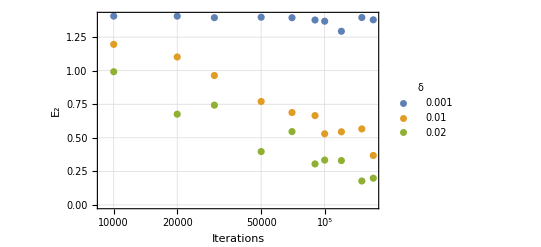

```mathematica
ListLogLinearPlot[{ergs4δp001, ergs4δp01, ergs4δp02}, PlotTheme->"Detailed", FrameLabel->{"Iterations", "E_2"}, FrameStyle->Black, 
			PlotLegends->PointLegend[{0.001,0.01,0.02},LegendLabel->"δ", LabelStyle->Black]]
```

```mathematica
Export["ergs1_forMH.pdf",%62]
```

ergs1_forMH.pdf

```mathematica
Export["ergs2_forMH.pdf",%63]
```

ergs2_forMH.pdf

### Segunda medición de ergodicidades para muestras MH

Para esta segunda medición se cuenta con 250 muestras: 5 valores distintos de deltas y betas con 10 valores distintos de N para cada combinación. Todas estas muestras se tomaron para r_z = 0.5 y p = 0.3.  (en realidad nomás son 249 muestras, pues la correspondiente a β = 1000, δ = 0.05 y N = 500 000 no alcanzó a salir...)

#### Generación de los datos de ergodicidad a graficar (a partir de las muestras)

```mathematica
SetDirectory["/media/storage/ciencia/investigacion/tesis/muestras_MH/distintasN_betasydeltas_Rp5_Pp3/samples"]
```

/media/storage/ciencia/investigacion/tesis/muestras_MH/distintasN_betasydeltas_Rp5_Pp3/samples

```mathematica
(*Esta función va importando muestras y calcula su vector D de mínimas distancias. No guarda la muestra, sólo el vector.
  La muestra se especifica con rz, swapP, β y δ. Se debe indicar la muestra brutal de referencia a usar y los tamaños de la
  muestra (enes)*)
minVecsForMHSample[enes_List, brutalRef_List, rz_, swapP_, β_, δ_]:= 
				MapMonitored[minDistancesVector[brutalRef, 
							 Get["MHsample_N="<>ToString[#]<>"_delta="<>ToString[δ]<>"_beta="<>ToString[β]<>"_rz="<>ToString[rz]<>"_p="<>ToString[swapP]<>".wl"][[2]]]&
							,enes]
```

```mathematica
deltas = {0.01, 0.02, 0.03, 0.04, 0.05};
betas = {100, 250, 400, 500, 1000};
enes = {10000, 20000, 40000, 60000, 80000, 100000, 200000,300000,400000,500000};
```

Generación de los vectores de mínimas distancias:

```mathematica
(*corrieron aquí mismo:*)
minVecsRp5Pp3β100 = MapMonitored[minVecsForMHSample[enes, brutalRefRp5Pp3, 0.5, 0.3, 100, #]&, deltas];
minVecsRp5Pp3β250 = MapMonitored[minVecsForMHSample[enes, brutalRefRp5Pp3, 0.5, 0.3, 250, #]&, deltas];
(*andan en el cluster corriendo:*)
(*minVecsRp5Pp3β400 = MapMonitored[minVecsForMHSample[enes, brutalRefRp5Pp3, 0.5, 0.3, 400, #]&, deltas];
minVecsRp5Pp3β500 = MapMonitored[minVecsForMHSample[enes, brutalRefRp5Pp3, 0.5, 0.3, 500, #]&, deltas];
minVecsRp5Pp3β1000 = Append[(MapMonitored[minVecsForMHSample[enes, brutalRefRp5Pp3, 0.5, 0.3, 1000, #]&, Drop[deltas,-1]]), 
							minVecsForMHSample[Drop[enes, -1], brutalRefRp5Pp3, 0.5, 0.3, 1000, 0.05]];*)
(*Para β=1000 se tiene distinto porque falta la muestra con β=1000, δ=0.05 y N=500 000*)

(*Importando lo que generó el cluster:*)
(*minVecsRp5Pp3β400 = Get["minVecsRp5Pp3_beta400.wl"];
minVecsRp5Pp3β500 = Get["minVecsRp5Pp3_beta500.wl"];
minVecsRp5Pp3β1000 = Get["minVecsRp5Pp3_beta1000.wl"];*)
```

Cálculo de las ergodicidades correspondientes:

```mathematica
(*beta = 100*)
ergs2Rp5Pp3β100 = Map[Map[ergodicityMeasure2[#]&, #]&, minVecsRp5Pp3β100];
ergs4Rp5Pp3β100 = Map[Map[ergodicityMeasure4[#]&, #]&, minVecsRp5Pp3β100];
(*beta = 250*)
ergs2Rp5Pp3β250 = Map[Map[ergodicityMeasure2[#]&, #]&, minVecsRp5Pp3β250];
ergs4Rp5Pp3β250 = Map[Map[ergodicityMeasure4[#]&, #]&, minVecsRp5Pp3β250];
(*beta = 400*)
ergs2Rp5Pp3β400 = Map[Map[ergodicityMeasure2[#]&, #]&, minVecsRp5Pp3β400];
ergs4Rp5Pp3β400 = Map[Map[ergodicityMeasure4[#]&, #]&, minVecsRp5Pp3β400];
(*beta = 500*)
ergs2Rp5Pp3β500 = Map[Map[ergodicityMeasure2[#]&, #]&, minVecsRp5Pp3β500];
ergs4Rp5Pp3β500 = Map[Map[ergodicityMeasure4[#]&, #]&, minVecsRp5Pp3β500];
(*beta = 1000*)
ergs2Rp5Pp3β1000 = Map[Map[ergodicityMeasure2[#]&, #]&, minVecsRp5Pp3β1000];
ergs4Rp5Pp3β1000 = Map[Map[ergodicityMeasure4[#]&, #]&, minVecsRp5Pp3β1000];
(*Todas estas ergodicidades ya se exportaron, por lo que no es necesario calcularlas de nuevo, sólo importarlas*)
```

```mathematica
(*En efecto, aquí las importamos en vez de calcularlas de nuevo (sólo se conservará usando la erg2):*)
SetDirectory["/media/storage/ciencia/investigacion/tesis/muestras_MH/distintasN_betasydeltas_Rp5_Pp3/ergs"];
(*beta = 100*)
ergs2Rp5Pp3β100 = <<"ergs2_Rp5Pp3_beta=100_alldeltas.wl";
(*beta = 250*)
ergs2Rp5Pp3β250 = <<"ergs2_Rp5Pp3_beta=250_alldeltas.wl";
(*beta = 400*)
ergs2Rp5Pp3β400 = <<"ergs2_Rp5Pp3_beta=400_alldeltas.wl";
(*beta = 500*)
ergs2Rp5Pp3β500 = <<"ergs2_Rp5Pp3_beta=500_alldeltas.wl";
(*beta = 1000*)
ergs2Rp5Pp3β1000 = <<"ergs2_Rp5Pp3_beta=1000_alldeltas.wl";
```

```mathematica
(*Aquí importamos la ergodicidades 4*)
SetDirectory["/media/storage/ciencia/investigacion/tesis/muestras_MH/distintasN_betasydeltas_Rp5_Pp3/ergs"];
(*beta = 100*)
ergs4Rp5Pp3β100 = <<"ergs4_Rp5Pp3_beta=100_alldeltas.wl";
(*beta = 250*)
ergs4Rp5Pp3β250 = <<"ergs4_Rp5Pp3_beta=250_alldeltas.wl";
(*beta = 400*)
ergs4Rp5Pp3β400 = <<"ergs4_Rp5Pp3_beta=400_alldeltas.wl";
(*beta = 500*)
ergs4Rp5Pp3β500 = <<"ergs4_Rp5Pp3_beta=500_alldeltas.wl";
(*beta = 1000*)
ergs4Rp5Pp3β1000 = <<"ergs4_Rp5Pp3_beta=1000_alldeltas.wl";
```

#### Graficación de los datos (Erg. 1)

```mathematica
betas = {100, 250, 400, 500, 1000};
enes = {10000, 20000, 40000, 60000, 80000, 100000, 200000, 300000, 400000, 500000};
deltas = Table[0.01 i, {i,5}];
```

```mathematica
colors=(("DefaultPlotStyle"/.(Method /. 
     Charting`ResolvePlotTheme["Scientific" ,  ListLogLogPlot]))/. Directive[x_,__]:>x)
```

{RGBColor[0.9, 0.36, 0.054],RGBColor[0.365248, 0.427802, 0.758297],RGBColor[0.945109, 0.593901, 0.],RGBColor[0.645957, 0.253192, 0.685109],RGBColor[0.285821, 0.56, 0.450773],RGBColor[0.7, 0.336, 0.],RGBColor[0.491486, 0.345109, 0.8],RGBColor[0.71788, 0.568653, 0.],RGBColor[0.70743, 0.224, 0.542415],RGBColor[0.287228, 0.490217, 0.664674],RGBColor[0.982289285128704, 0.5771321368979874, 0.011542503255145636],RGBColor[0.5876740325800278, 0.2877284499870081, 0.7500695697462922],RGBColor[0.4262088601796793, 0.5581552810007578, 0.2777996730417023],RGBColor[0.9431487543762861, 0.414555896337833, 0.07140829055870854],RGBColor[0.41497437140121635, 0.393632147507352, 0.7842993779115092]}

```mathematica
(*Primero generamos los datos, es decir, los ponemos en forma*)
ergs2δp01allβ = List[ergs2Rp5Pp3β100[[1]], ergs2Rp5Pp3β250[[1]], ergs2Rp5Pp3β400[[1]], ergs2Rp5Pp3β500[[1]],ergs2Rp5Pp3β1000[[1]]];
ergs2δp02allβ = List[ergs2Rp5Pp3β100[[2]], ergs2Rp5Pp3β250[[2]], ergs2Rp5Pp3β400[[2]], ergs2Rp5Pp3β500[[2]],ergs2Rp5Pp3β1000[[2]]];
ergs2δp03allβ = List[ergs2Rp5Pp3β100[[3]], ergs2Rp5Pp3β250[[3]], ergs2Rp5Pp3β400[[3]], ergs2Rp5Pp3β500[[3]],ergs2Rp5Pp3β1000[[3]]];
ergs2δp04allβ = List[ergs2Rp5Pp3β100[[4]], ergs2Rp5Pp3β250[[4]], ergs2Rp5Pp3β400[[4]], ergs2Rp5Pp3β500[[4]],ergs2Rp5Pp3β1000[[4]]];
ergs2δp05allβ = List[ergs2Rp5Pp3β100[[5]], ergs2Rp5Pp3β250[[5]], ergs2Rp5Pp3β400[[5]], ergs2Rp5Pp3β500[[5]],ergs2Rp5Pp3β1000[[5]]];
```

```mathematica
erg2Dataδp01allβ = Map[MapThread[{#1,#2}&, {enes, #}]&, ergs2δp01allβ];
erg2Dataδp02allβ = Map[MapThread[{#1,#2}&, {enes, #}]&, ergs2δp02allβ];
erg2Dataδp03allβ = Map[MapThread[{#1,#2}&, {enes, #}]&, ergs2δp03allβ];
erg2Dataδp04allβ = Map[MapThread[{#1,#2}&, {enes, #}]&, ergs2δp04allβ];
erg2Dataδp05allβ = Append[Map[MapThread[{#1,#2}&, {enes, #}]&, Drop[ergs2δp05allβ,-1]], 
						 MapThread[{#1,#2}&, {Drop[enes,-1], ergs2δp05allβ[[5]]}]];
```

```mathematica
allDataForErg2βforeachδ = {erg2Dataδp01allβ, erg2Dataδp02allβ, erg2Dataδp03allβ, erg2Dataδp04allβ, erg2Dataδp05allβ};
```

```mathematica
legend1 = LineLegend[colors, MaTeX[betas, FontSize->18], LegendLabel->MaTeX["\\beta", Preamble->{"\\usepackage{newtxmath}"}, FontSize->18]]
```

```mathematica
(*distintas betas para cada delta*)
plotsDeltas = MapThread[Show[ListLogLogPlot[#1, PlotLabel->MaTeX["\\delta = "<>ToString[#2], Preamble->{"\\usepackage{newtxmath}"}], PlotTheme->"Scientific", 
							FrameLabel->MaTeX[{"\\text{Iteraciones}", "E_1"}, Preamble->{"\\usepackage{newtxmath}"}],
							FrameStyle->Black,
							PlotRange->{0.02, 0.9}, Joined->True, Mesh->All, MeshStyle->PointSize[0.014],GridLines->Automatic], 
			  LogPlot[0.1, {x,0,500000}, PlotStyle->{Red, Dashed}]]&, 
		 {allDataForErg2βforeachδ, deltas}];
```

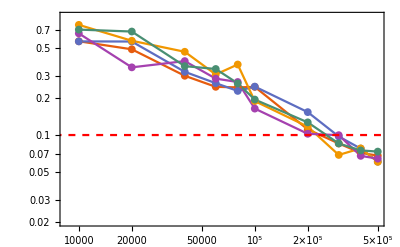
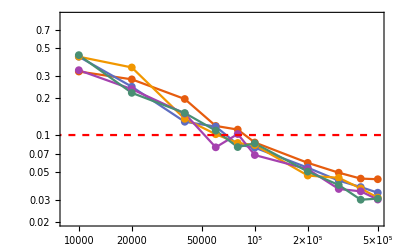
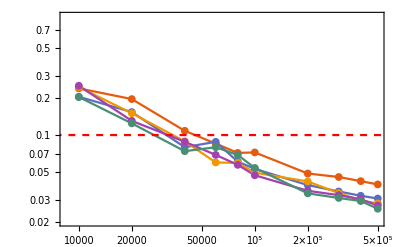
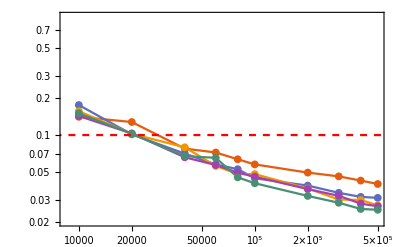
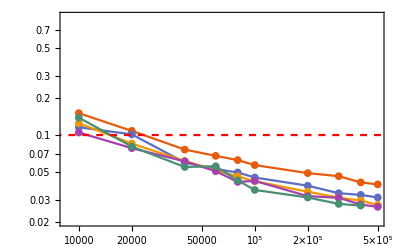
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- |

```mathematica
Grid[{plotsDeltas[[1;;2]],
	  plotsDeltas[[3;;4]],
	  {plotsDeltas[[5]], legend1}
}, ItemSize->Automatic, ItemStyle->ImageSizeMultipliers->1, Spacings->{1, 1}]
```

```mathematica
Export["ergsVSiterations_diffBetasDeltas_Rp5Pp3.pdf", %206]
```

ergsVSiterations_diffBetasDeltas_Rp5Pp3.pdf

Para saber cuál es el mínimo número de iteraciones necesarias para alcanzar la ergodicidad óptima se realizarán ajustes a los datos que tomen los valores con una β para la cual la ergodicidad ya no quede influida (o sea β =400). Se tomará entonces la intersección de la recta ajustada con la línea E_1=0.1.

```mathematica
(*ajustes de los datos, para encontrar la intersección más exacta con la línea Subscript[E, 1] = 0.1 (la roja)*)
fitδp01 = FindFit[Log@erg2Dataδp01allβ[[2]], m x + b, {m, b},{x}];
fitδp02 = FindFit[Log@erg2Dataδp02allβ[[2]], m x + b, {m, b},{x}];
fitδp03 = FindFit[Log@erg2Dataδp03allβ[[2]], m x + b, {m, b},{x}];
fitδp04 = FindFit[Log@erg2Dataδp04allβ[[2]], m x + b, {m, b},{x}];
fitδp05 = FindFit[Log@erg2Dataδp05allβ[[2]], m x + b, {m, b},{x}];
```

```mathematica
colors
```

{RGBColor[0.9, 0.36, 0.054],RGBColor[0.365248, 0.427802, 0.758297],RGBColor[0.945109, 0.593901, 0.],RGBColor[0.645957, 0.253192, 0.685109],RGBColor[0.285821, 0.56, 0.450773],RGBColor[0.7, 0.336, 0.],RGBColor[0.491486, 0.345109, 0.8],RGBColor[0.71788, 0.568653, 0.],RGBColor[0.70743, 0.224, 0.542415],RGBColor[0.287228, 0.490217, 0.664674],RGBColor[0.982289285128704, 0.5771321368979874, 0.011542503255145636],RGBColor[0.5876740325800278, 0.2877284499870081, 0.7500695697462922],RGBColor[0.4262088601796793, 0.5581552810007578, 0.2777996730417023],RGBColor[0.9431487543762861, 0.414555896337833, 0.07140829055870854],RGBColor[0.41497437140121635, 0.393632147507352, 0.7842993779115092]}

```mathematica
fitplots = MapThread[Show[ListLogLogPlot[#1, PlotLabel->MaTeX["\\delta = "<>ToString[#2]<>",\\,\\,\\beta=250", Preamble->{"\\usepackage{newtxmath}"}], PlotTheme->"Scientific",
										PlotStyle->colors[[2]],
										FrameLabel->MaTeX[{"\\text{Iteraciones}\\,\\,(N)", "E_1"}, Preamble->{"\\usepackage{newtxmath}"}],
										FrameStyle->Black, GridLines->Automatic],
										LogLogPlot[0.1, {x,0,500000}, PlotStyle->{Red, Dashed}],
										LogLogPlot[Exp[b] x^m /. #3,{x,0,500000}, PlotStyle->{colors[[3]], Thickness[0.004]}]]&, 
			{{erg2Dataδp01allβ[[2]], erg2Dataδp02allβ[[2]], erg2Dataδp03allβ[[2]], erg2Dataδp04allβ[[2]], erg2Dataδp05allβ[[2]]}, deltas, {fitδp01, fitδp02, fitδp03, fitδp04, fitδp05}}];
```

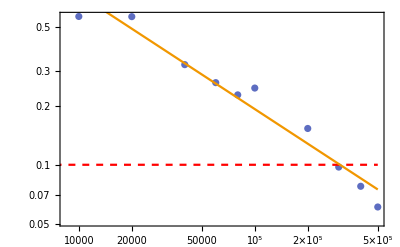

```mathematica
fitplots[[1]]
```

```mathematica
SetDirectory["/media/storage/ciencia/investigacion/tesis/muestras_MH"]
```

/media/storage/ciencia/investigacion/tesis/muestras_MH

```mathematica
Export["lineFit_deltap01_Rp5Pp3.pdf", %268]
```

lineFit_deltap01_Rp5Pp3.pdf

```mathematica
(*teniendo las ecuaciones de los ajustes, en qué punto tenemeos E = 0.1 ?*)
Map[Solve[(Exp[b] x^m /. #) == 0.1, x]&, {fitδp01, fitδp02, fitδp03, fitδp04, fitδp05}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of Solve::ifun will be suppressed during this calculation.

{{{x→305027.}},{{x→77195.}},{{x→36563.}},{{x→21545.9}},{{x→12747.2}}}

Acá vamos a graficar los mismos datos pero al revés: Para cada beta, ponemos distintas deltas. Quizá esta forma de ver los datos no nos sea tan útil como la anterior.

```mathematica
(*Acá se grafican al revés: dstinitas deltas, para cada beta.*)
erg2Dataβ100allδ = Map[MapThread[{#1,#2}&, {enes, #}]&, ergs2Rp5Pp3β100];
erg2Dataβ250allδ = Map[MapThread[{#1,#2}&, {enes, #}]&, ergs2Rp5Pp3β250];
erg2Dataβ400allδ = Map[MapThread[{#1,#2}&, {enes, #}]&, ergs2Rp5Pp3β400];
erg2Dataβ500allδ = Map[MapThread[{#1,#2}&, {enes, #}]&, ergs2Rp5Pp3β500];
erg2Dataβ1000allδ = Append[Map[MapThread[{#1,#2}&, {enes, #}]&, Drop[ergs2Rp5Pp3β1000,-1]], 
						 MapThread[{#1,#2}&, {Drop[enes,-1], ergs2Rp5Pp3β1000[[5]]}]];
```

```mathematica
allDataForErg2δforeachβ = {erg2Dataβ100allδ, erg2Dataβ250allδ, erg2Dataβ400allδ, erg2Dataβ500allδ, erg2Dataβ1000allδ};
```

```mathematica
legend = LineLegend[colors, MaTeX[deltas, FontSize->17], LegendLabel->MaTeX["\\delta", FontSize->17], LegendLayout->"Row"]
```

```mathematica
(*distintas deltas para cada beta*)
plots = MapThread[Show[ListLogLogPlot[#1, PlotLabel->MaTeX["\\beta = "<>ToString[#2], Preamble->{"\\usepackage{newtxmath}"}], PlotTheme->"Scientific", 
							FrameLabel->MaTeX[{"\\text{Iteraciones}", "E_1"}, Preamble->{"\\usepackage{newtxmath}"}],
							FrameStyle->Black,
							PlotRange->Full, GridLines->Automatic, Joined->True, Mesh->All, MeshStyle->PointSize[0.014]],
				LogPlot[0.1, {x, 0, 500000}, PlotStyle->{Red, Dashed}]]&, 
		 {allDataForErg2δforeachβ, betas}];
```

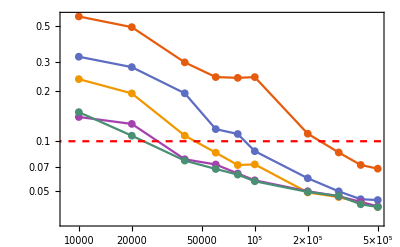
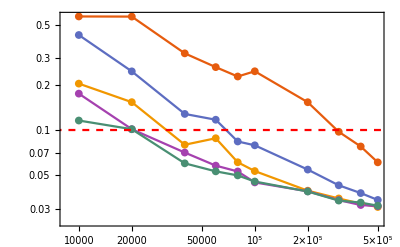
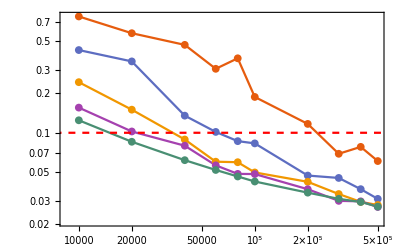
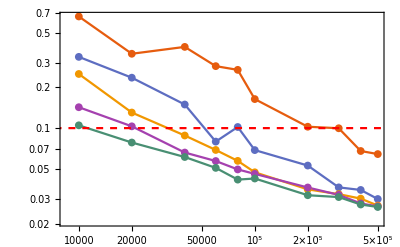
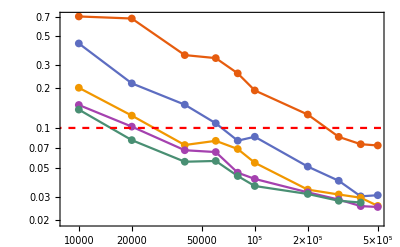
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- |

```mathematica
Grid[{plots[[1;;2]],
	  plots[[3;;4]],
	  {plots[[5]], legend}
}, ItemSize->Automatic, ItemStyle->ImageSizeMultipliers->1, Spacings->{1, 1}]
```

```mathematica
SetDirectory["/media/storage/ciencia/investigacion/tesis/muestras_MH"]
```

/media/storage/ciencia/investigacion/tesis/muestras_MH

```mathematica
Export["ergsVSiterations_diffBetasDeltas_Rp5Pp3.pdf", %155]
```

ergsVSiterations_diffBetasDeltas_Rp5Pp3.pdf

#### ¿La ergodicidad 1 depende de β?

```mathematica
(*ERGODICIDAD 1*)
ergVSbetaδ1 = Map[MapThread[{#1, #2}&, {betas, #}]&, Transpose[#[[1]]& /@ {ergs2Rp5Pp3β100, ergs2Rp5Pp3β250, ergs2Rp5Pp3β400, ergs2Rp5Pp3β500, ergs2Rp5Pp3β1000}]];
ergVSbetaδ2 = Map[MapThread[{#1, #2}&, {betas, #}]&, Transpose[#[[2]]& /@ {ergs2Rp5Pp3β100, ergs2Rp5Pp3β250, ergs2Rp5Pp3β400, ergs2Rp5Pp3β500, ergs2Rp5Pp3β1000}]];
ergVSbetaδ3 = Map[MapThread[{#1, #2}&, {betas, #}]&, Transpose[#[[3]]& /@ {ergs2Rp5Pp3β100, ergs2Rp5Pp3β250, ergs2Rp5Pp3β400, ergs2Rp5Pp3β500, ergs2Rp5Pp3β1000}]];
ergVSbetaδ4 = Map[MapThread[{#1, #2}&, {betas, #}]&, Transpose[#[[4]]& /@ {ergs2Rp5Pp3β100, ergs2Rp5Pp3β250, ergs2Rp5Pp3β400, ergs2Rp5Pp3β500, ergs2Rp5Pp3β1000}]];
ergVSbetaδ5 = Join[Map[MapThread[{#1, #2}&, {betas, #}]&, 
				  MapThread[#1~Join~{#2} &, {Transpose[#[[5]]& /@ {ergs2Rp5Pp3β100, ergs2Rp5Pp3β250, ergs2Rp5Pp3β400, ergs2Rp5Pp3β500}][[1;;9]], ergs2Rp5Pp3β1000[[5]]}]],
				  {MapThread[{#1, #2}&, {betas[[1;;4]], Transpose[#[[5]]& /@ {ergs2Rp5Pp3β100, ergs2Rp5Pp3β250, ergs2Rp5Pp3β400, ergs2Rp5Pp3β500}][[10]]}]}];
```

```mathematica
data = {ergVSbetaδ1, ergVSbetaδ2, ergVSbetaδ3, ergVSbetaδ4, ergVSbetaδ5};
leg = LineLegend[colors, MaTeX[{"10\\,000", "20\\,000", "40\\,000", "60\\,000","80\\,000", "10^5", "2\\times 10^5", "3\\times 10^5", "4\\times 10^5", "5\\times 10^5"}], 
				 LegendLabel->MaTeX["N", Preamble->{"\\usepackage{newtxmath}"}], LegendLayout->"Row"]
```

```mathematica
plotsErgVSbeta = MapThread[Show[ListLogPlot[#1, PlotLabel->MaTeX["\\delta = "<>ToString[#2], Preamble->{"\\usepackage{newtxmath}"}], 
				           PlotTheme->"Scientific",
				           Joined->True, Mesh->All, MeshStyle->PointSize[0.014], GridLines->Automatic, 
				           FrameStyle->Black,
				           FrameLabel->MaTeX[{"\\text{Estrechez}\\,\\,(\\beta)", "E_1"}, Preamble->{"\\usepackage{newtxmath}"}]],
				           LogPlot[0.1, {x,0,1000}, PlotStyle->{Red,Dashed}]]&, 
		                  {data, deltas}];
```

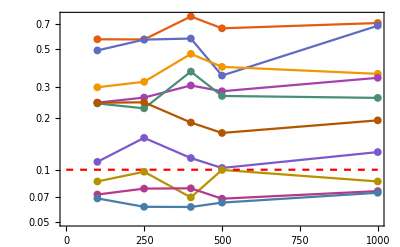
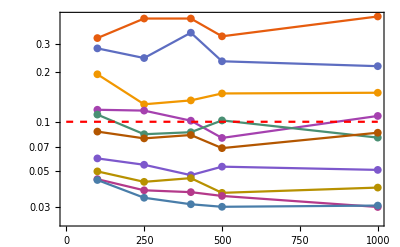
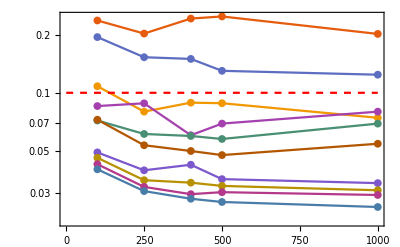
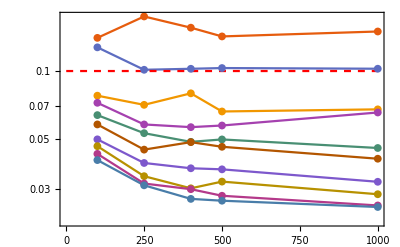
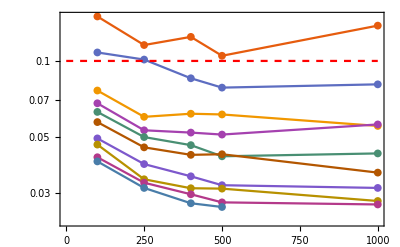
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- |

```mathematica
Grid[{plotsErgVSbeta[[1;;2]],
	  plotsErgVSbeta[[3;;4]],
	  {plotsErgVSbeta[[5]], leg}
}, ItemStyle->ImageSizeMultipliers->1, Spacings->{1, 1}]
```

```mathematica
SetDirectory["/media/storage/ciencia/investigacion/tesis/muestras_MH"]
```

/media/storage/ciencia/investigacion/tesis/muestras_MH

```mathematica
Export["ergVSBeta_distDeltasN_Rp5Pp3.pdf", %144]
```

ergVSBeta_distDeltasN_Rp5Pp3.pdf

```mathematica
betas
```

{100,250,400,500,1000}

#### ¿La ergodicidad 2 depende de β?

```mathematica
(*ERGODICIDAD 2*)
erg4VSbetaδ1 = Map[MapThread[{#1, #2}&, {betas, #}]&, Transpose[#[[1]]& /@ {ergs4Rp5Pp3β100, ergs4Rp5Pp3β250, ergs4Rp5Pp3β400, ergs4Rp5Pp3β500, ergs4Rp5Pp3β1000}]];
erg4VSbetaδ2 = Map[MapThread[{#1, #2}&, {betas, #}]&, Transpose[#[[2]]& /@ {ergs4Rp5Pp3β100, ergs4Rp5Pp3β250, ergs4Rp5Pp3β400, ergs4Rp5Pp3β500, ergs4Rp5Pp3β1000}]];
erg4VSbetaδ3 = Map[MapThread[{#1, #2}&, {betas, #}]&, Transpose[#[[3]]& /@ {ergs4Rp5Pp3β100, ergs4Rp5Pp3β250, ergs4Rp5Pp3β400, ergs4Rp5Pp3β500, ergs4Rp5Pp3β1000}]];
erg4VSbetaδ4 = Map[MapThread[{#1, #2}&, {betas, #}]&, Transpose[#[[4]]& /@ {ergs4Rp5Pp3β100, ergs4Rp5Pp3β250, ergs4Rp5Pp3β400, ergs4Rp5Pp3β500, ergs4Rp5Pp3β1000}]];
erg4VSbetaδ5 = Join[Map[MapThread[{#1, #2}&, {betas, #}]&, 
				  MapThread[#1~Join~{#2} &, {Transpose[#[[5]]& /@ {ergs4Rp5Pp3β100, ergs4Rp5Pp3β250, ergs4Rp5Pp3β400, ergs4Rp5Pp3β500}][[1;;9]], ergs4Rp5Pp3β1000[[5]]}]],
				  {MapThread[{#1, #2}&, {betas[[1;;4]], Transpose[#[[5]]& /@ {ergs4Rp5Pp3β100, ergs4Rp5Pp3β250, ergs4Rp5Pp3β400, ergs4Rp5Pp3β500}][[10]]}]}];
```

```mathematica
data2 = {erg4VSbetaδ1, erg4VSbetaδ2, erg4VSbetaδ3, erg4VSbetaδ4, erg4VSbetaδ5};
leg = LineLegend[colors, enes, LegendLabel->"N", LegendLayout->"Row"];
```

```mathematica
plotsErg4VSbeta = MapThread[ListPlot[#1, PlotLabel->MaTeX["\\delta = "<>ToString[#2], Preamble->{"\\usepackage{newtxmath}"}], 
				                     PlotTheme->"Scientific",
				                     Joined->True, Mesh->All, MeshStyle->PointSize[0.014], GridLines->Automatic,
				                     FrameLabel->MaTeX[{"\\beta", "E_2"}, Preamble->{"\\usepackage{newtxmath}"}]]&, 
		                   {data2, deltas}];
```

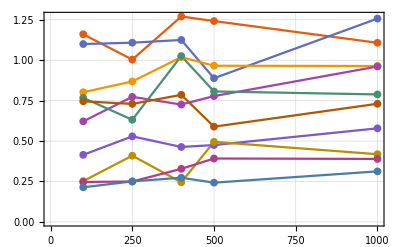
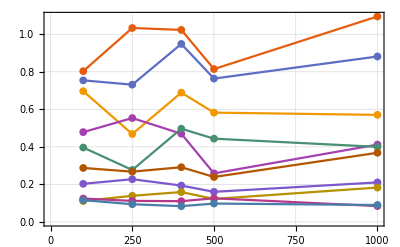
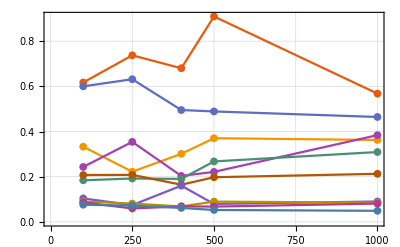
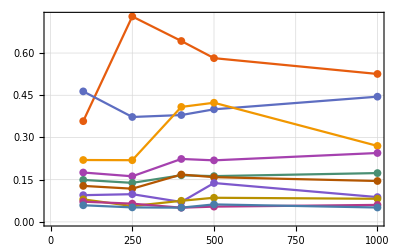
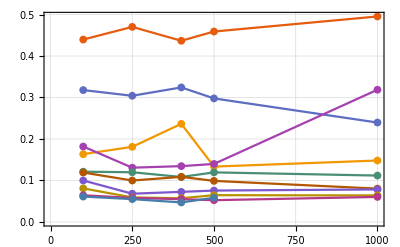
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- |

```mathematica
Grid[{plotsErg4VSbeta[[1;;2]],
	  plotsErg4VSbeta[[3;;4]],
	  {plotsErg4VSbeta[[5]], leg}
}, ItemStyle->ImageSizeMultipliers->1, Spacings->{1, 1}]
```

```mathematica
Export["erg2.pdf", %388]
```

erg2.pdf

## Juegos

### Generando ilustraciones

```mathematica
enes = {10000, 15000, 20000, 25000, 30000, 35000, 40000,45000,50000, 55000};
```

```mathematica
gamesamples = Get["MHsample_N="<>ToString[#]<>"_rz=0.5_p=0.3.wl"][[2]]& /@ {10000, 25000, 40000, 55000};
```

```mathematica
Grid[{{visualizeBipartiteSystem[gamesamples[[1]]], visualizeBipartiteSystem[gamesamples[[2]]]},
	  {Style[Text["N = 10000"],Black], Style[Text["N = 25000"],Black]},
	  {visualizeBipartiteSystem[gamesamples[[3]]], visualizeBipartiteSystem[gamesamples[[4]]]},
	  {Style[Text["N = 40000"],Black], Style[Text["N = 55000"],Black]}
}]
```

-Graphics3D- | -Graphics3D-
N = 10000 | N = 25000
-Graphics3D- | -Graphics3D-
N = 40000 | N = 55000

```mathematica
Export["ergodic_spheres.pdf", %13]
```

ergodic_spheres.pdf

### Juegos con el estado promedio analítico

```mathematica
enes = {10000, 20000, 30000, 50000, 70000, 90000, 100000, 120000, 150000, 170000};
analyticAverage = ρaverageTwoQubitsbasiscomp[0.3, 0.5]; (*edo. promedio analítico para p = 0.3 y rz = 0.5*)
```

```mathematica
SetDirectory["/media/storage/ciencia/trabajo-con-carlos/tesis/muestras_MH/distintasN_beta500_delta0p02"]
mhAveragesδ0p02 = MapMonitored[preimageMean[Get["MHsample_N="<>ToString[#]<>"_delta=0.02_rz=0.5_p=0.3.wl"][[2]]]&, enes];
```

/media/storage/ciencia/trabajo-con-carlos/tesis/muestras_MH/distintasN_beta500_delta0p02

```mathematica
SetDirectory["/media/storage/ciencia/trabajo-con-carlos/tesis/muestras_MH/distintasN_beta500_delta0p01"]
mhAveragesδ0p01 = MapMonitored[preimageMean[Get["MHsample_N="<>ToString[#]<>"_rz=0.5_p=0.3.wl"][[2]]]&, enes];
```

/media/storage/ciencia/trabajo-con-carlos/tesis/muestras_MH/distintasN_beta500_delta0p01

```mathematica
SetDirectory["/media/storage/ciencia/trabajo-con-carlos/tesis/muestras_MH/distintasN_beta500_delta0p05"]
mhAveragesδ0p05 = MapMonitored[preimageMean[Get["MHsample_N="<>ToString[#]<>"_delta=0.05_rz=0.5_p=0.3.wl"][[2]]]&, Drop[Drop[enes, -2], {2}]];
```

/media/storage/ciencia/trabajo-con-carlos/tesis/muestras_MH/distintasN_beta500_delta0p05

```mathematica
SetDirectory["/media/storage/ciencia/trabajo-con-carlos/tesis/muestras_MH/distintasN_beta500_delta0p001"]
mhAveragesδ0p001 = MapMonitored[preimageMean[Get["MHsample_N="<>ToString[#]<>"_delta=0.001_rz=0.5_p=0.3.wl"][[2]]]&, enes];
```

/media/storage/ciencia/trabajo-con-carlos/tesis/muestras_MH/distintasN_beta500_delta0p001

```mathematica
fidelityDataδ0p02 = MapThread[{#1, #2}&, {enes, Map[fidelity[analyticAverage, mhAveragesδ0p02[[#]]]&, Table[i,{i,Length[mhAveragesδ0p02]}]]}];
fidelityDataδ0p01 = MapThread[{#1, #2}&, {enes, Map[fidelity[analyticAverage, mhAveragesδ0p01[[#]]]&, Table[i,{i,Length[mhAveragesδ0p01]}]]}];
fidelityDataδ0p05 = MapThread[{#1, #2}&, {Drop[Drop[enes,-2],{2}], Map[fidelity[analyticAverage, mhAveragesδ0p05[[#]]]&, Table[i,{i,Length[mhAveragesδ0p05]}]]}];
fidelityDataδ0p001 = MapThread[{#1, #2}&, {enes, Map[fidelity[analyticAverage, mhAveragesδ0p001[[#]]]&, Table[i,{i,Length[mhAveragesδ0p001]}]]}];
```

```mathematica
deltas = {0.001, 0.01, 0.02, 0.05};
```

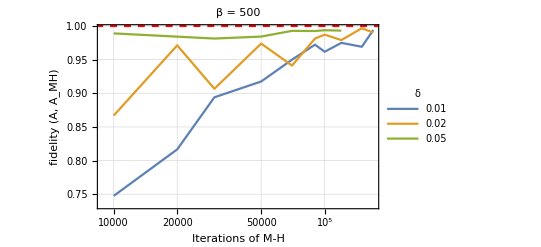

```mathematica
Show[ListLogLinearPlot[{fidelityDataδ0p01, fidelityDataδ0p02, fidelityDataδ0p05}, PlotTheme->"Detailed", 
					   FrameLabel->{"Iterations of M-H", "fidelity (A, A_MH)"},
					   PlotLabel->"β = 500",
					   PlotLegends->PointLegend[Drop[deltas, 1], LegendLabel->δ],
					   Joined->True], 
	 Plot[1, {x,0,170000}, PlotStyle->{Red, Dashed}]]
```

### ¿Qué pasa si la referencia brutal tiene más estados?

```mathematica
Directory[]
```

/media/storage/ciencia/investigacion/tesis/muestras_MH/distintasN_betasydeltas_Rp5_Pp3/samples

```mathematica
betas
```

{100,250,400,500,1000}

```mathematica
(*preimagenes*)
samplesδ1 = Get["MHsample_N=10000_delta=0.01_beta="<>ToString[#]<>"_rz=0.5_p=0.3.wl"][[2]]& /@ betas;
samplesδ2 = Get["MHsample_N=10000_delta=0.02_beta="<>ToString[#]<>"_rz=0.5_p=0.3.wl"][[2]]& /@ betas;
samplesδ3 = Get["MHsample_N=10000_delta=0.03_beta="<>ToString[#]<>"_rz=0.5_p=0.3.wl"][[2]]& /@ betas;
samplesδ4 = Get["MHsample_N=10000_delta=0.04_beta="<>ToString[#]<>"_rz=0.5_p=0.3.wl"][[2]]& /@ betas;
samplesδ5 = Get["MHsample_N=10000_delta=0.05_beta="<>ToString[#]<>"_rz=0.5_p=0.3.wl"][[2]]& /@ betas;
```

```mathematica
Dimensions[brutalRefRp5Pp3]
```

{500,4,4}

```mathematica
minVecsδ1 = MapMonitored[minDistancesVector[brutalRefRp5Pp3, #]&, samplesδ1];
minVecsδ2 = MapMonitored[minDistancesVector[brutalRefRp5Pp3, #]&, samplesδ2];
minVecsδ3 = MapMonitored[minDistancesVector[brutalRefRp5Pp3, #]&, samplesδ3];
minVecsδ4 = MapMonitored[minDistancesVector[brutalRefRp5Pp3, #]&, samplesδ4];
minVecsδ5 = MapMonitored[minDistancesVector[brutalRefRp5Pp3, #]&, samplesδ5];
```

```mathematica
ergDataδ1 = MapThread[{#1, #2}&, {betas, (ergodicityMeasure2[#]& /@ minVecsδ1)}];
ergDataδ2 = MapThread[{#1, #2}&, {betas, (ergodicityMeasure2[#]& /@ minVecsδ2)}];
ergDataδ3 = MapThread[{#1, #2}&, {betas, (ergodicityMeasure2[#]& /@ minVecsδ3)}];
ergDataδ4 = MapThread[{#1, #2}&, {betas, (ergodicityMeasure2[#]& /@ minVecsδ4)}];
ergDataδ5 = MapThread[{#1, #2}&, {betas, (ergodicityMeasure2[#]& /@ minVecsδ5)}];
```

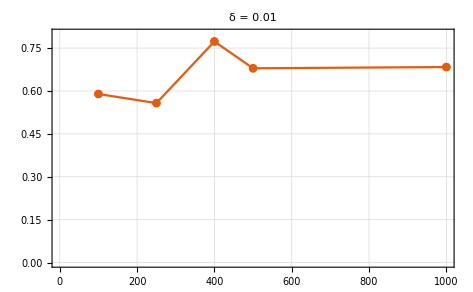
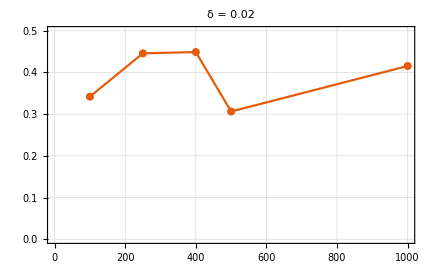
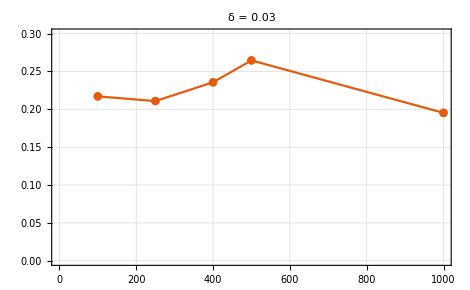
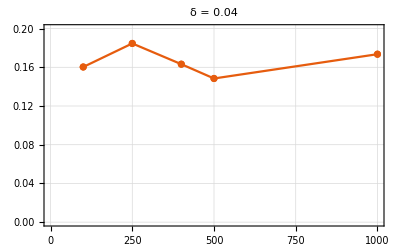
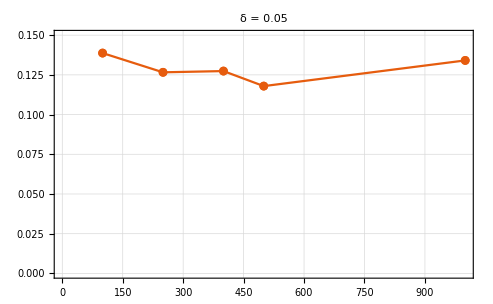

```mathematica
MapThread[ListPlot[#1, PlotLabel->"δ = "<>ToString[#2], PlotTheme->"Scientific", Joined->True, PlotRange->{0, #3}, GridLines->Automatic, Mesh->Full]&, 
{{ergDataδ1, ergDataδ2, ergDataδ3, ergDataδ4, ergDataδ5}, deltas, {0.8, 0.5, 0.3, 0.2, 0.15}}]
```